```mathematica
Clear["Global`*"];
ŠtejTakePiksleOkol[slikapiksli_,baarva_,ϵ_,sred_,polm_]:={
resx=Length[slikapiksli[[1]]  ];
resy=Length[slikapiksli];
Δnaštetih=0;
Δvsotatakih={0,0,0};
Δvsotakord={0,0};
(*koordinate pikslov na kvadratnici*)

levo=If[polm≥sred[[2]],1,sred[[2]]-polm  ];
desno=If[sred[[2]]+polm>resx,resx,sred[[2]]+polm ];
gor=If[polm≥sred[[1]],1,sred[[1]]-polm];
dol=If[sred[[1]]+polm>resy,resy,sred[[1]]+polm];
kpnk=If[polm==0,
{sred},
Flatten[
{
Table[
{dol,x},
{x,levo,desno-1}],
Table[
{y,desno},
{y,gor+1,dol}],
Table[
{gor,x},
{x,levo+1,desno}],
Table[
{y,levo},
{y,gor,dol-1}]
},
1]
];
Do[
{i1,i2}=kpnk[[i]];
If[

Normalize[baarva].Normalize[slikapiksli[[i1,i2]]  ]>1-ϵ,
(*Total[slikapiksli[[i1,i2]]]<2.1*)

Δnaštetih++;
Δvsotatakih+=slikapiksli[[i1,i2]];
Δvsotakord+={i1,i2};
(*zadnji tak piksel*)
ztp={i1,i2};
],
{i,Length[kpnk]}];
Δnaštetih
}[[1]];
Novosred[slikapiksli_,baarva_,ϵ_,sred_]:={
Clear[ztp];
polmer=0;
While[Not[ListQ[ztp]],
ŠtejTakePiksleOkol[slikapiksli,baarva,ϵ,sred,polmer];
polmer++
];
ztp
}[[1]];
TežPike[slikapiksli_,baarva_,ϵ_,sred_]:={
polmer=0;
Δnaštetih=1000000000;
naštetih=0;
vsotatakih={0,0,0};
vsotakord={0,0};(*kordinat pikslov*)
While[Δnaštetih≠0,
Δvsotatakih={0,0,0};
Δvsotakord={0,0};
ŠtejTakePiksleOkol[slikapiksli,baarva,ϵ,sred,polmer];
naštetih+=Δnaštetih;
vsotatakih+=Δvsotatakih;
vsotakord+=Δvsotakord;
polmer++
];
barva=vsotatakih/naštetih;
N[vsotakord/naštetih]
}[[1]];
```

```mathematica
mapaslik="c:\\Users\\gal\\Downloads\\tetraeder\\";
(*seznam poti do slik*)
spds=FileNames[All,mapaslik];
slika1=Import[spds[[1]]  ];
slika1piksli=(Delete[#,-1]&/@#)&/@ImageData[slika1];
DynamicModule[{leganasliki=1/10 Length[slika1piksli]{{1,1},{2,2},{3,3}}},
{
LocatorPane[Dynamic[leganasliki],slika1],
Dynamic[
MatrixForm[barve0=(slika1piksli[[-#[[2]],#[[1]] ]])&/@Round[Reverse[leganasliki]] ] ],
Dynamic[MatrixForm[sred0=Round[leganasliki]]]
}

]
```

```mathematica
spds=FileNames[All,mapaslik];
barva=barve0[[1]];
sred=Round[sred0[[1]] ];
ϵ=.0005;
stopnjapolinoma=5;
polinom=Total[
Table[
ToExpression["par"<>ToString[i]]*τ^i,
{i,0,stopnjapolinoma}]
];
parametri=Table[
ToExpression["par"<>ToString[i]],
{i,0,stopnjapolinoma}];
prejšnjih10sred={};
dokam=0;
lege=Table[
dokam++;
slika=Import[spds[[i]]  ];
slikapiksli=(Delete[#,-1]&/@#)&/@ImageData[slika];
AppendTo[prejšnjih10sred,sred];

If[
i>10,
prejšnjih10sred=Delete[prejšnjih10sred,1];
sred=((
nparametri=FindFit[
#,
polinom,
parametri,
τ
];
polinom/.nparametri
)/.τ->11)&/@Transpose[prejšnjih10sred];
sred=Round[sred];
];
sred=TežPike[slikapiksli,barva,ϵ,
Novosred[slikapiksli,barva,ϵ,sred]];
sred=Round[sred],



{i,1000}]
```

{{180,457},{181,455},{270,457},{270,454},{272,452},{274,449},{275,447},{276,446},{278,445},{280,443},{281,443},{282,442},{283,442},{283,442},{284,442},{284,442},{284,442},{284,443},{285,443},{285,444},{285,445},{286,447},{286,448},{286,449},{287,451},{287,453},{288,454},{288,456},{288,458},{288,460},{287,462},{286,464},{286,466},{285,467},{285,470},{285,471},{285,473},{285,475},{285,476},{286,478},{286,479},{286,480},{286,481},{287,482},{287,483},{287,483},{287,484},{288,485},{288,486},{287,486},{287,486},{287,486},{287,487},{286,486},{286,486},{286,487},{286,486},{286,486},{285,486},{284,485},{284,485},{283,484},{282,484},{281,483},{280,482},{280,481},{280,480},{280,479},{279,479},{278,478},{277,477},{276,476},{275,475},{274,475},{272,474},{271,473},{271,472},{270,471},{270,470},{270,469},{270,469},{270,468},{270,467},{270,467},{269,466},{269,466},{269,466},{268,466},{268,466},{268,466},{267,465},{266,465},{266,465},{266,466},{266,466},{265,466},{264,466},{263,467},{263,468},{262,469},{261,469},{260,470},{259,471},{258,472},{257,472},{255,473},{254,474},{252,475},{251,476},{250,477},{248,478},{246,479},{244,480},{242,481},{240,482},{238,483},{237,483},{235,485},{234,486},{232,487},{230,487},{229,488},{228,488},{227,489},{227,490},{226,490},{225,491},{224,492},{224,493},{223,493},{223,494},{223,494},{224,495},{224,495},{225,496},{225,496},{225,497},{226,497},{226,497},{226,497},{226,497},{224,497},{222,498},{221,498},{221,498},{221,498},{220,498},{220,497},{220,497},{219,496},{219,495},{219,495},{218,493},{219,492},{219,491},{219,490},{220,489},{220,487},{221,486},{222,484},{224,483},{226,481},{227,480},{229,478},{230,476},{230,475},{231,473},{231,471},{231,469},{232,467},{232,466},{232,464},{231,462},{231,461},{231,459},{231,458},{231,456},{232,455},{231,454},{231,452},{231,451},{230,450},{230,449},{230,448},{230,448},{230,448},{230,447},{229,447},{229,448},{229,448},{229,448},{228,449},{228,450},{227,450},{227,451},{227,452},{226,453},{227,454},{227,456},{227,458},{227,459},{227,461},{228,463},{228,464},{228,466},{229,468},{228,470},{228,472},{228,474},{228,476},{228,478},{228,480},{228,482},{227,484},{226,485},{225,487},{224,489},{222,490},{222,491},{222,492},{223,493},{223,494},{223,495},{223,495},{222,495},{222,495},{222,495},{222,495},{222,494},{222,493},{222,493},{222,492},{222,491},{224,489},{223,488},{224,486},{225,484},{225,482},{226,480},{226,479},{227,476},{228,473},{229,471},{229,468},{231,466},{232,463},{232,461},{234,458},{234,456},{236,453},{237,451},{238,449},{238,447},{239,445},{239,444},{239,443},{240,441},{240,441},{239,441},{238,440},{238,438},{238,438},{237,438},{238,438},{237,438},{237,439},{237,439},{236,440},{236,441},{236,442},{236,444},{236,446},{236,447},{236,449},{235,451},{235,453},{235,455},{235,457},{235,460},{236,462},{235,464},{235,466},{235,468},{234,470},{234,472},{234,474},{233,476},{233,479},{233,480},{233,482},{232,484},{232,486},{232,487},{232,488},{232,488},{232,489},{232,489},{232,491},{231,491},{232,491},{231,490},{232,490},{231,489},{232,488},{231,488},{231,486},{231,485},{232,484},{232,482},{232,482},{233,480},{233,479},{233,479},{233,476},{234,475},{234,473},{234,472},{235,471},{237,468},{236,466},{237,463},{237,461},{237,458},{237,456},{238,455},{238,452},{238,450},{238,449},{237,447},{237,446},{237,444},{237,443},{237,442},{237,441},{238,440},{238,440},{237,440},{237,440},{238,440},{239,441},{241,441},{242,442},{243,443},{245,445},{245,446},{246,448},{247,451},{249,453},{250,456},{252,459},{252,463},{252,467},{253,470},{253,474},{254,478},{255,482},{256,487},{256,491},{256,496},{256,500},{257,504},{256,510},{256,513},{254,517},{254,521},{255,522},{245,525},{240,525},{241,517},{233,525},{205,573},{236,559},{237,562},{298,510},{237,544},{243,552},{249,558},{249,559},{319,521},{245,549},{245,554},{247,556},{246,556},{316,504},{250,543},{244,543},{247,540},{250,538},{249,539},{253,540},{262,548},{256,548},{268,534},{262,533},{261,524},{253,514},{251,504},{250,498},{251,492},{251,487},{250,482},{251,477},{250,472},{250,468},{250,463},{250,459},{250,456},{250,452},{250,449},{250,447},{249,445},{249,443},{249,441},{249,440},{249,439},{248,438},{248,438},{248,438},{247,438},{247,438},{246,439},{246,440},{246,441},{245,443},{245,445},{244,447},{244,449},{243,452},{242,455},{241,458},{241,461},{240,464},{239,467},{239,470},{239,474},{238,477},{239,480},{239,484},{238,486},{237,488},{237,490},{236,491},{234,492},{230,496},{225,491},{220,484},{219,485},{235,494},{227,505},{233,508},{234,512},{233,516},{233,514},{232,516},{232,514},{232,515},{232,514},{234,513},{233,515},{235,512},{235,512},{239,511},{245,512},{240,522},{242,515},{248,509},{248,505},{242,501},{242,495},{240,489},{238,485},{237,482},{236,477},{235,474},{235,470},{234,466},{234,463},{234,459},{233,456},{233,453},{233,450},{233,447},{233,445},{233,443},{233,441},{234,439},{234,438},{234,437},{234,436},{234,436},{234,436},{234,436},{234,436},{234,436},{234,437},{234,437},{235,438},{235,440},{236,441},{236,443},{236,445},{236,447},{236,450},{236,452},{237,456},{236,459},{236,462},{236,465},{235,468},{235,471},{234,475},{233,477},{232,480},{231,484},{228,487},{226,489},{224,492},{221,494},{219,497},{216,497},{213,498},{211,500},{209,504},{207,502},{198,499},{202,497},{198,503},{199,504},{198,511},{200,513},{201,517},{201,518},{203,518},{206,518},{209,519},{213,517},{217,516},{223,515},{229,510},{235,510},{242,508},{249,506},{256,505},{264,504},{269,500},{276,497},{280,495},{286,492},{292,491},{295,489},{299,487},{301,485},{303,483},{305,481},{306,479},{307,477},{307,476},{307,475},{306,474},{305,472},{304,471},{302,470},{300,469},{299,469},{297,469},{294,468},{292,467},{289,467},{286,467},{283,467},{279,467},{276,467},{272,468},{268,468},{263,468},{259,469},{255,469},{250,470},{245,471},{240,471},{236,473},{231,474},{227,475},{222,476},{218,477},{214,479},{211,479},{207,481},{204,482},{202,483},{201,484},{200,485},{199,486},{199,486},{200,487},{201,488},{202,488},{204,489},{206,489},{209,489},{213,489},{216,488},{219,488},{223,487},{226,486},{230,486},{234,487},{238,486},{242,486},{246,486},{249,486},{252,486},{254,485},{256,485},{258,485},{259,485},{260,484},{261,483},{261,482},{261,481},{261,480},{261,478},{260,477},{259,475},{260,474},{259,472},{259,470},{258,468},{258,466},{258,465},{257,464},{256,462},{255,460},{255,459},{254,457},{254,456},{253,454},{252,453},{250,452},{249,451},{248,450},{246,450},{244,450},{243,449},{241,448},{239,448},{238,448},{236,448},{235,448},{233,449},{231,450},{230,451},{230,452},{229,454},{228,455},{227,456},{227,458},{226,460},{226,462},{226,464},{226,466},{227,469},{228,471},{229,473},{231,476},{232,478},{234,481},{236,483},{239,486},{240,488},{242,489},{244,491},{246,493},{248,495},{251,496},{253,498},{254,499},{257,500},{258,501},{259,502},{261,503},{262,503},{264,502},{263,503},{265,503},{266,502},{266,500},{266,498},{265,498},{266,497},{265,495},{265,495},{266,494},{267,493},{266,490},{265,490},{264,488},{263,485},{264,484},{263,482},{262,479},{262,477},{261,473},{261,470},{260,466},{259,462},{260,458},{260,455},{261,452},{260,448},{260,445},{261,442},{261,439},{262,437},{262,435},{262,433},{262,432},{262,431},{261,430},{261,430},{261,430},{260,430},{259,430},{259,430},{258,431},{258,432},{257,432},{257,434},{257,436},{256,438},{256,440},{256,443},{255,445},{255,448},{254,451},{254,453},{253,456},{253,460},{253,463},{252,466},{252,469},{252,472},{252,475},{252,479},{251,482},{251,485},{251,488},{251,491},{250,493},{250,495},{250,497},{250,498},{250,499},{250,501},{250,502},{249,503},{249,504},{249,505},{249,505},{248,505},{248,506},{248,506},{248,506},{247,506},{247,506},{246,506},{246,506},{246,505},{246,504},{246,503},{246,502},{246,501},{246,499},{247,498},{246,496},{246,495},{246,494},{247,492},{247,491},{247,489},{248,487},{248,486},{248,485},{249,483},{250,482},{250,481},{250,479},{250,478},{250,477},{250,476},{249,476},{249,475},{249,474},{249,474},{249,474},{249,473},{249,474},{249,474},{249,474},{249,475},{250,476},{250,476},{250,477},{250,479},{250,480},{250,481},{250,482},{250,483},{250,485},{250,486},{249,488},{249,490},{249,492},{249,494},{249,496},{249,499},{249,501},{249,503},{249,505},{248,508},{248,510},{248,513},{248,514},{248,516},{248,518},{249,517},{248,523},{247,524},{246,523},{246,527},{243,530},{240,526},{245,525},{247,528},{243,530},{246,533},{244,535},{250,539},{250,544},{247,546},{244,543},{243,543},{245,544},{249,546},{248,545},{248,538},{249,532},{248,530},{249,526},{248,524},{249,522},{248,518},{248,514},{249,511},{250,506},{250,501},{252,498},{253,495},{255,491},{256,487},{258,482},{260,478},{262,475},{264,471},{266,468},{268,464},{270,461},{271,459},{272,457},{272,455},{272,454},{272,453},{272,452},{272,450},{272,450},{272,449},{272,449},{271,450},{270,451},{270,452},{270,453},{269,454},{268,456},{267,458},{266,460},{264,463},{263,465},{262,468},{261,470},{260,473},{259,476},{258,480},{257,482},{257,485},{257,488},{257,491},{258,493},{258,496},{259,498},{260,501},{261,503},{262,505},{264,508},{266,510},{268,512},{270,513},{272,515},{275,516},{277,518},{279,519},{280,520},{281,521},{282,521},{283,521},{283,521},{283,521},{283,521},{282,520},{282,519},{281,518},{279,517},{278,515},{276,514},{273,511},{272,511},{270,509},{268,508},{266,506},{264,505},{261,502},{259,501},{257,499},{254,497},{252,495},{249,493},{245,491},{242,490},{238,488},{234,488},{231,488},{228,488},{226,488},{223,487},{221,488},{219,490},{216,491},{214,492},{211,492},{210,492},{208,493},{206,493},{205,494},{205,495},{204,495},{204,495},{204,496},{204,498},{204,498},{206,500},{206,501},{207,502},{208,503},{210,504},{212,505},{213,506},{215,506},{218,506},{221,507},{221,508},{223,509},{222,509},{225,508},{224,506},{226,508},{226,511},{230,512},{230,513},{232,513},{233,513},{236,516},{236,517},{237,516},{239,515},{237,515},{238,513},{240,512},{241,512},{244,511},{244,512},{244,511},{247,510},{247,511},{249,508},{249,508},{251,506},{248,505},{249,508},{250,507},{247,503},{246,505}}

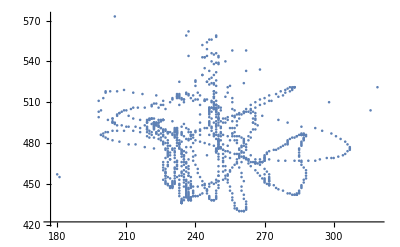

```mathematica
ListPlot[%]
```

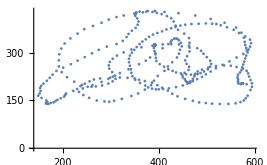

```mathematica
ListPlot[%24]
```